## Dispersion spiral

```mathematica
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
A[kx_,ky_,δ_]=0.25*((4-2*γ[kx,ky])*0.5(Cos[δ]+1)+2*γ[kx,ky]+(2-Cos[kx])*Sin[δ]*Tan[δ]);
B[kx_,ky_,δ_]=0.25*(2*(γ[kx,ky]*0.5*(1+Cos[δ])+γ[kx,ky]+0.5Cos[kx]*Sin[δ]*Tan[δ]));
ϵ[kx_,ky_,δ_]=Sqrt[A[kx,ky,ArcTan[δ]]^2-B[kx,ky,ArcTan[δ]]^2];
```

```mathematica
Liste={};
NN=2^5;
Table[AppendTo[Liste,ϵ[kx,kx,δ]],{kx,0,π,π/(NN*Sqrt[2])}];
Table[AppendTo[Liste,ϵ[π-kx,π,δ]],{kx,0,π,π/NN}];
Table[AppendTo[Liste,ϵ[kx,π-kx,δ]],{kx,0,π,π/(NN*Sqrt[2])}];
Table[AppendTo[Liste,ϵ[π-kx,0,δ]],{kx,0,π,π/NN}];
```

```mathematica
GammaP=0+1;
MP=Ceiling[NN*Sqrt[2]]+1;
XPrimeP=MP+NN;
XP=XPrimeP+MP;
GammaPrimeP=XP+NN;
```

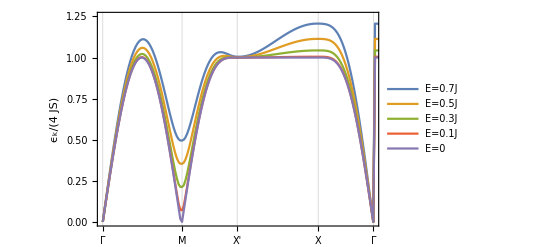

```mathematica
ListLinePlot[{Liste/.δ-> 0.7,Liste/.δ-> 0.5,Liste/.δ->0.3,Liste/.δ-> 0.1,Liste/.δ-> 0},Frame->True,FrameTicks->{{Automatic,None},{{{GammaP,"Γ"},{MP,"M"},{XPrimeP,"X'"},{XP,"X"},{GammaPrimeP,"Γ"}},None}},PlotRange->{{1,GammaPrimeP},{0,1.25}},PlotLegends->{"E=0.7J","E=0.5J","E=0.3J","E=0.1J","E=0"},GridLines->{{GammaP,MP,XPrimeP,XP,GammaPrimeP},None},FrameLabel->{None,Subscript[ϵ, k]/(4JS)}]
```

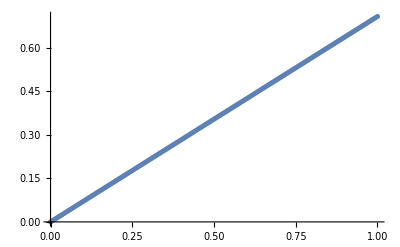

```mathematica
gaplist=Table[{d,ϵ[π,π,d]},{d,0,1,0.005}];
ListPlot[gaplist]
```

```mathematica
Plot3D[{0,ϵ[x,y,0.25]},{x,-2π,2π},{y,-2π,2π}]
```

-Graphics3D-

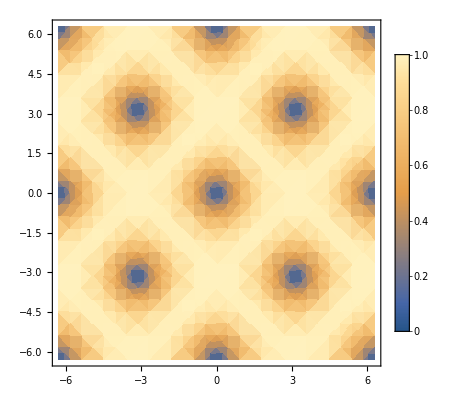

```mathematica
DensityPlot[ϵ[x,y,0.0],{x,-2π,2π},{y,-2π,2π},PlotLegends->Automatic]
```

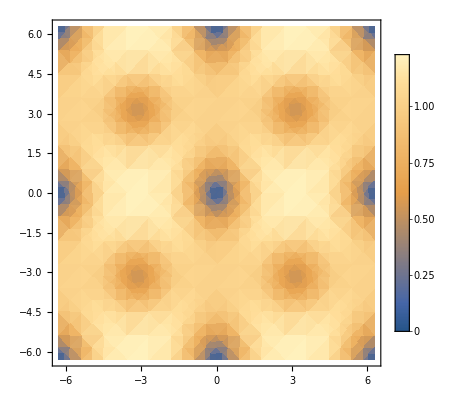

```mathematica
DensityPlot[ϵ[x,y,0.75],{x,-2π,2π},{y,-2π,2π},PlotLegends->Automatic]
```

## Ground state energy

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Clear[dx];
J=1;
Lx=16;
Ly=16;
r0={1,0};
r1={0,1};
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
S[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
border=0;
BulkBonds=DeleteCases[Flatten[Table[If[i<j&&l[[i,1]]≥border&&l[[i,2]]>=border&&l[[i,1]]<Lx-border&&l[[i,2]]<Ly-border&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
Bonds=BulkBonds;
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dx,0,0}],{i,1,Length[Bonds]}];
NeelEnergylist={};
SpiralEnergylist={};
NumericEnergylist={};
Energylist={};
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
Neelstatearglist=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2,{i,1,Lx*Ly}]},1];
energyNeel=N[Hnew/.Neelstatearglist/.dx->0];
For[d=0,d<100,d=d+1,
dx=d/100;
(*Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];*)
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
BKList=Table[Flatten[{ϕlist,θlist}]⟦i⟧->Flatten[{plist,tlist}][[i]],{i,Length[ϕlist]+Length[θlist]}];
spiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-0*l⟦i⟧⟦1⟧*ArcTan[dx]+l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListspiral=Flatten[{Table[ϕlist⟦i⟧->-π/2,{i,1,Length[ϕlist]}],Table[θlist⟦i⟧->spiraltlist⟦i⟧,{i,Length[θlist]}]}];
AppendTo[Energylist,{dx,energyNeel,N[Hnew/.BKList],
N[Hnew/.BKListspiral]}];
]
```

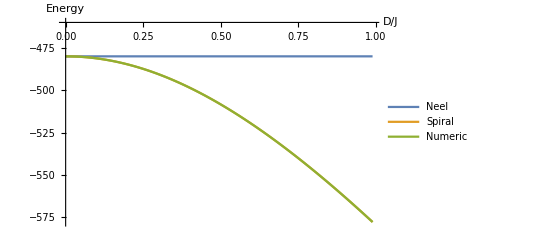

```mathematica
ListLinePlot[{Table[{Energylist⟦i⟧⟦1⟧,Energylist⟦i⟧⟦2⟧},{i,1,Length[Energylist]}],Table[{Energylist⟦i⟧⟦1⟧,Energylist⟦i⟧⟦3⟧},{i,1,Length[Energylist]}],Table[{Energylist⟦i⟧⟦1⟧,Energylist⟦i⟧⟦4⟧},{i,1,Length[Energylist]}]},AxesOrigin->{0,-460},AxesLabel->{"D/J","Energy"},PlotLegends->{"Neel","Spiral","Numeric"}]
```